Kendall tau comparison with null model

## Setup

```mathematica
(* set directory *)
SetDirectory["/Users/tbury/Google Drive/Research/doctorate/critical_transitions_18/fisheries"];
```

```mathematica
(* Good fonts *)
TMBFS10={FontFamily->"Helvetica",FontSize->10};
TMBFS12={FontFamily->"Helvetica",FontSize->12};
TMBFS15={FontFamily->"Helvetica",FontSize->15};
TMBbold={FontFamily->"Helvetica",FontSize->15,Bold};
(* Neat colours *)
TMBcolours=ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

### Import data

```mathematica
dirNameNull="ricker_null_sigma0p04";
dataDirNull="data_export/"<>dirNameNull;
```

```mathematica
dirNameFold="ricker_fold_sigma0p04";
dataDirFold="data_export/"<>dirNameFold;
```

```mathematica
dirNameFlip="ricker_flip_sigma0p04";
dataDirFlip="data_export/"<>dirNameFlip;
```

```mathematica
(* Import Kendall tau values *)
ktauNullData=Import[dataDirNull<>"/ktau.csv"];
ktauFoldData=Import[dataDirFold<>"/ktau.csv"];
ktauFlipData=Import[dataDirFlip<>"/ktau.csv"];
```

### Figure params

```mathematica
imgs=200;
```

```mathematica
binWidth=0.2;
```

```mathematica
plRange={{-1,1},{0,100}};
```

## Computing p-values

We compute the p value as the probability that the null model gives a Kendall tau value as strong or stronger than the flip/fold model.

## Figures

### Variance

```mathematica
label="Variance";
```

```mathematica
indexNull=Position[ktauNullData[[1]],label][[1,1]];
indexFold=Position[ktauFoldData[[1]],label][[1,1]];
indexFlip=Position[ktauFlipData[[1]],label][[1,1]];
```

```mathematica
ktauValsNull=ktauNullData[[2;;,indexNull]];
ktauValsFold=ktauFoldData[[2;;,indexFold]];
ktauValsFlip=ktauFlipData[[2;;,indexFlip]];
```

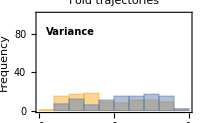

```mathematica
figVarFold=Histogram[{ktauValsNull,ktauValsFold},{binWidth},
PlotRange->plRange,
ImageSize->imgs,
Frame->True,
FrameLabel->{{"Frequency",""},{"",""}},
ChartLegends->Placed[{Style["Null",10],Style["Fold",10]},Scaled[{0.8,0.7}]],
ImagePadding->{{50,20},{20,10}},
PlotLabel->"Fold trajectories",
Epilog->Text[Style["Variance",10,Bold],Scaled[{0.22,0.8}]]]
```

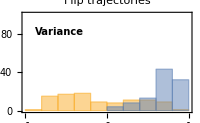

```mathematica
figVarFlip=Histogram[{ktauValsNull,ktauValsFlip},{binWidth},
PlotRange->plRange,
ImageSize->imgs,
Frame->True,
FrameLabel->{{"",""},{"",""}},
ChartLegends->Placed[{Style["Null",10],Style["Flip",10]},Scaled[{0.8,0.7}]],
ImagePadding->{{50,20},{20,10}},
PlotLabel->"Flip trajectories",
Epilog->Text[Style["Variance",10,Bold],Scaled[{0.22,0.8}]]]
```

### Smax

```mathematica
label="Smax";
```

```mathematica
indexNull=Position[ktauNullData[[1]],label][[1,1]];
indexFold=Position[ktauFoldData[[1]],label][[1,1]];
indexFlip=Position[ktauFlipData[[1]],label][[1,1]];
```

```mathematica
ktauValsNull=ktauNullData[[2;;,indexNull]];
ktauValsFold=ktauFoldData[[2;;,indexFold]];
ktauValsFlip=ktauFlipData[[2;;,indexFlip]];
```

```mathematica
(* make values that are equal to 1 0.99999, to keep in range 0<x<1 *)
ktauValsFlip=ktauValsFlip/.x_/;x>=1->0.999;
```

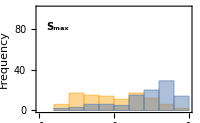

```mathematica
figSmaxFold=Histogram[{ktauValsNull,ktauValsFold},{binWidth},
PlotRange->plRange,
ImageSize->imgs,
Frame->True,
FrameLabel->{{"Frequency",""},{"",""}},
ImagePadding->{{50,20},{20,10}},
Epilog->Text[Style["S_max",10,Bold],Scaled[{0.14,0.8}]]]
```

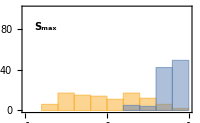

```mathematica
figSmaxFlip=Histogram[{ktauValsNull,ktauValsFlip},{binWidth},
PlotRange->plRange,
ImageSize->imgs,
Frame->True,
FrameLabel->{{"",""},{"",""}},
ImagePadding->{{50,20},{20,10}},
Epilog->Text[Style["S_max",10,Bold],Scaled[{0.14,0.8}]]]
```

### Lag-1 AC

```mathematica
label="Lag-1 AC";
```

```mathematica
indexNull=Position[ktauNullData[[1]],label][[1,1]];
indexFold=Position[ktauFoldData[[1]],label][[1,1]];
indexFlip=Position[ktauFlipData[[1]],label][[1,1]];
```

```mathematica
ktauValsNull=ktauNullData[[2;;,indexNull]];
ktauValsFold=ktauFoldData[[2;;,indexFold]];
ktauValsFlip=ktauFlipData[[2;;,indexFlip]];
```

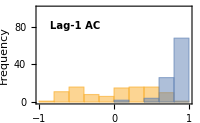

```mathematica
figAcFold=Histogram[{ktauValsNull,ktauValsFold},{binWidth},
PlotRange->plRange,
ImageSize->imgs,
Frame->True,
FrameLabel->{{"Frequency",""},{"Kendall τ",""}},
ImagePadding->{{50,20},{40,10}},
Epilog->Text[Style["Lag-1 AC",10,Bold],Scaled[{0.25,0.8}]]]
```

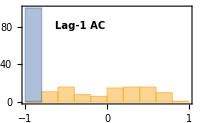

```mathematica
figAcFlip=Histogram[{ktauValsNull,ktauValsFlip},{binWidth},
PlotRange->plRange,
ImageSize->imgs,
Frame->True,
FrameLabel->{{"",""},{"Kendall τ",""}},
ImagePadding->{{50,20},{40,10}},
Epilog->Text[Style["Lag-1 AC",10,Bold],Scaled[{0.34,0.8}]]]
```

### Combine

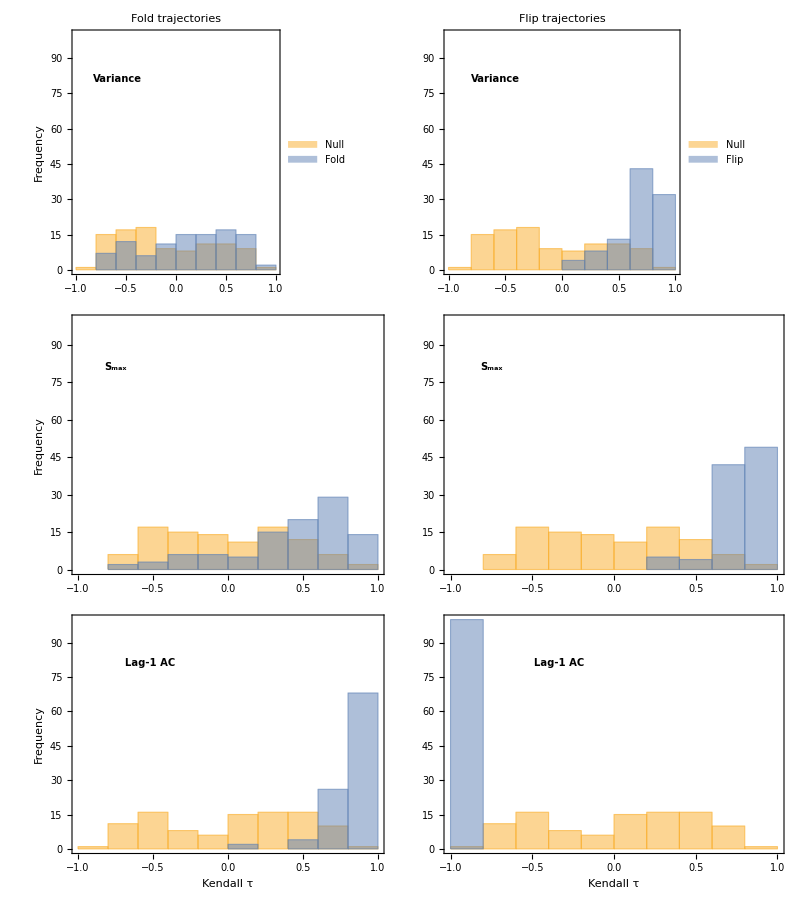

```mathematica
Grid[{{figVarFold,figVarFlip},{figSmaxFold,figSmaxFlip},{figAcFold,figAcFlip}},Spacings->{-2,-0.5}]
```